# Ant System TSP

```mathematica
ClearAll["Global`*"]
```

#### Code explanation

To run the code, simply execute the entire notebook. All the parameters of the simulation can be edited by changing the values in the section Simulation parameters. Explanation of the paramters:

tspFileName: The name of the TSP example to test. The TSP examples reside in the subdirectory “./TSP” of the notebook. For each TSP example, there are two files. The first file being the setup of the problem, and the second being the optimal route.

c: The trace base-line that will be added to all the edges at the beginning of the simulation.
α: A parameter that influences the importance of trace in the probability calculation of the movement of the ants.
β: A parameter that influences the importance of visibility in the probability calculation of the movement of the ants. The visibility of an edge is the reciprocal of its weight (i.e the visibility between towns i and j is the reciprocal of the distance between them).
Q: Affects the amount of trace that is added on to each edge, at the end of a cycle.
ρ: A multiplicative factor that will set the rate of decay of the trace at each edge (ρ = 1 → no decay).
simulationRuns: The amount of cycles that the simulation will run.

Graphs of the performance of the algorithm will be generated in the section Visualise results. The shortest path found in the algorithm, compared with the optimal path, will be shown in the section Path visualisations.

#### Simulation parameters

```mathematica
tspFileName = "gr666";
c = 0.01;
α = 1.0;
β = 4.0;
Q = 1.0;
ρ = 0.5;

simulationRuns = 109;
```

#### Functions

```mathematica
SetDirectory[NotebookDirectory[]];
link = Install["bin/tsp_ants_mathematica"]

GetDistanceAt[i_, j_] := edges[[Max[{i, j}], Min[{i, j}]]]
GetVisibilityAt[i_, j_] := 1.0/edges[[Max[{i, j}], Min[{i, j}]]]

GetPathLength[townlist_] :=
 Sum[ GetDistanceAt[townlist[[i]], townlist[[i+1]]],{i, 1, Length[townlist]-1}]

GetAntPaths[cycles_] := Map[Partition[#, GetNumberOfTowns[] + 1] &, Partition[GetAntPathHistories[], (GetNumberOfTowns[] + 1)*cycles]]

GetAntPathLengths[cycles_] := Partition[GetAntPathLengthHistories[], cycles]

RunSimulation[cycles_] :=Module[
{
cyclesLeft = cycles,
pathHistory = {},
pathLengths = {},
pathLenghtsData = {},
shortestPathLengths = {},
},

UpdateSimulation[cycles];
pathHistory = GetAntPaths[cycles] // Transpose;
pathLengths = Map[GetPathLength, pathHistory, {2}];
shortestPathLengths = Map[Min, pathLengths];

{GetEdgeTraces[], pathHistory, pathLengths, shortestPathLengths}
]
```

LinkObject[…]

#### Load TSP file

```mathematica
FullMatrixTspToEdges[tspFile_] := Map[ToExpression[StringSplit[#]] &, tspFile] //N;

NodesTspToEdges[tspFile_] := Module[
{ nodes = Map[ {ToExpression[#[[2]]], ToExpression[#[[3]]]} &,  Map[StringSplit, tspFile]] },
Table[ Norm[ nodes[[i]] - nodes[[j]] ] // N, {i, 1, Length[nodes]}, {j, 1,Length[nodes]}]
]

tspFile = Import["TSP/" <> tspFileName <> ".tsp", "Text"];
tspFile = StringSplit[tspFile, "\n"];
tspFileType = First[tspFile];
tspFile = Rest[tspFile];

edges = Switch[ tspFileType,
"FULL_MATRIX", FullMatrixTspToEdges[tspFile],
"NODE_COORD_SECTION", NodesTspToEdges[tspFile]
];
tspShortestCycleFile = Import["TSP/" <> tspFileName <> ".opt.tour", "Text"];
knownShortestPath = Map[ToExpression, StringSplit[tspShortestCycleFile]];
AppendTo[knownShortestPath, knownShortestPath[[1]]];

knownShortestPathLength = GetPathLength[knownShortestPath];
numOfTowns = Length[edges];
```

#### Run Simulation

```mathematica
edgesFlat = Flatten[edges];
StartSimulation[edgesFlat,c //N, α//N, β//N, Q//N, ρ//N];
Do[AddAnt[i - 1], {i, 1, numOfTowns}];
```

```mathematica
res = RunSimulation[simulationRuns];
```

#### Visualise results

Best path: 3794.27

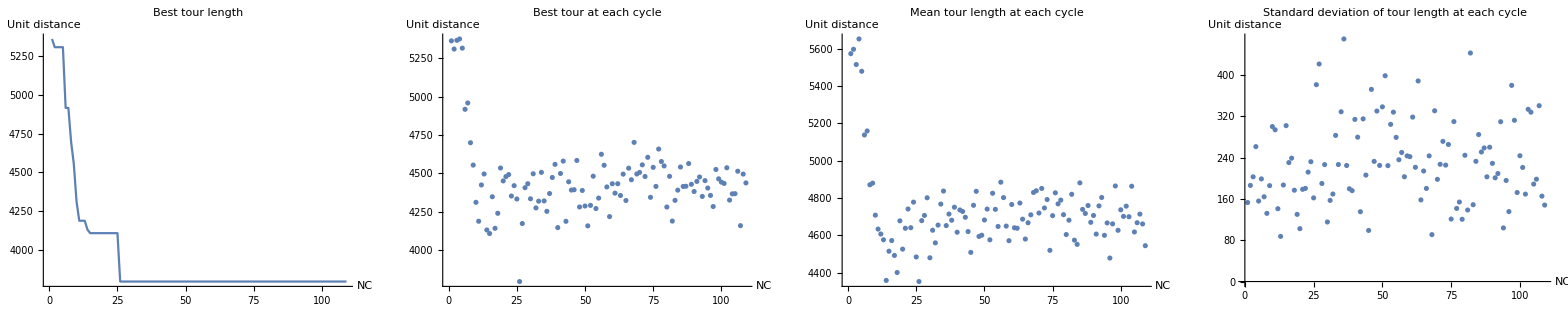

```mathematica
edgeTraces = res[[1]];
pathHistory = res[[2]];
pathLengths = res[[3]];
shortestPathLengths = res[[4]];

Print["Best path: " <> ToString[Min[shortestPathLengths]]]

(*
plotlabeladd = "\n" <> tspFileName <> ToString[StringForm[": c=``, α=``, β=`` Q=``, ρ=``, t=``", c, α, β, Q, ρ, simulationRuns]];

roundToLowest = {a___, b_, c_, d___} /;b<c-> {a, b,b, d};
shortestPathLengthsRounded = shortestPathLengths //. roundToLowest;
bestTourLengthPlot = ListPlot[shortestPathLengthsRounded, PlotLabel->"Best tour length" <> plotlabeladd, PlotRange->All, Joined->True];

bestTourLengthAtCyclePlot=ListPlot[shortestPathLengths, PlotLabel->"Best tour at each cycle" <> plotlabeladd, PlotRange->All];

meanTourLengthPlot = ListPlot[Mean /@ pathLengths, PlotLabel->"Mean tour length at each cycle" <> plotlabeladd, PlotRange->All];
stdDevPlot = ListPlot[StandardDeviation /@ pathLengths, PlotLabel->"Standard deviation of tour length at each cycle" <> plotlabeladd, PlotRange->All];

GraphicsRow[bestTourLengthPlot, bestTourLengthAtCyclePlot, meanTourLengthPlot, stdDevPlot]
*)

plotlabeladd = tspFileName <> ToString[StringForm[": c=``, α=``, β=`` Q=``, ρ=``, NC_max=``", c, α, β, Q, ρ, simulationRuns]];

plotLabelDirective = Directive[Black, FontSize-> 14];

roundToLowest = {a___, b_, c_, d___} /;b<c-> {a, b,b, d};
shortestPathLengthsRounded = shortestPathLengths //. roundToLowest;
bestTourLengthPlot = ListPlot[shortestPathLengthsRounded, PlotLabel->"Best tour length", LabelStyle-> plotLabelDirective, PlotRange->All, Joined->True, AxesLabel -> {"NC", "Unit distance"}];

bestTourLengthAtCyclePlot=ListPlot[shortestPathLengths, PlotLabel->"Best tour at each cycle", LabelStyle-> plotLabelDirective, PlotRange->All, AxesLabel -> {"NC", "Unit distance"}];

meanTourLengthPlot = ListPlot[Mean /@ pathLengths, PlotLabel->"Mean tour length at each cycle", LabelStyle-> plotLabelDirective, PlotRange->All, AxesLabel ->{"NC", "Unit distance"}];
stdDevPlot = ListPlot[StandardDeviation /@ pathLengths, PlotLabel->"Standard deviation of tour length at each cycle", LabelStyle-> plotLabelDirective, PlotRange->All, AxesLabel ->{"NC", "Unit distance"}];

GraphicsRow[{bestTourLengthPlot, bestTourLengthAtCyclePlot, meanTourLengthPlot, stdDevPlot}, ImageSize->Full, PlotLabel-> plotlabeladd, LabelStyle->Directive[Bold,Black, FontSize-> 15]]
```

#### Path visualisations

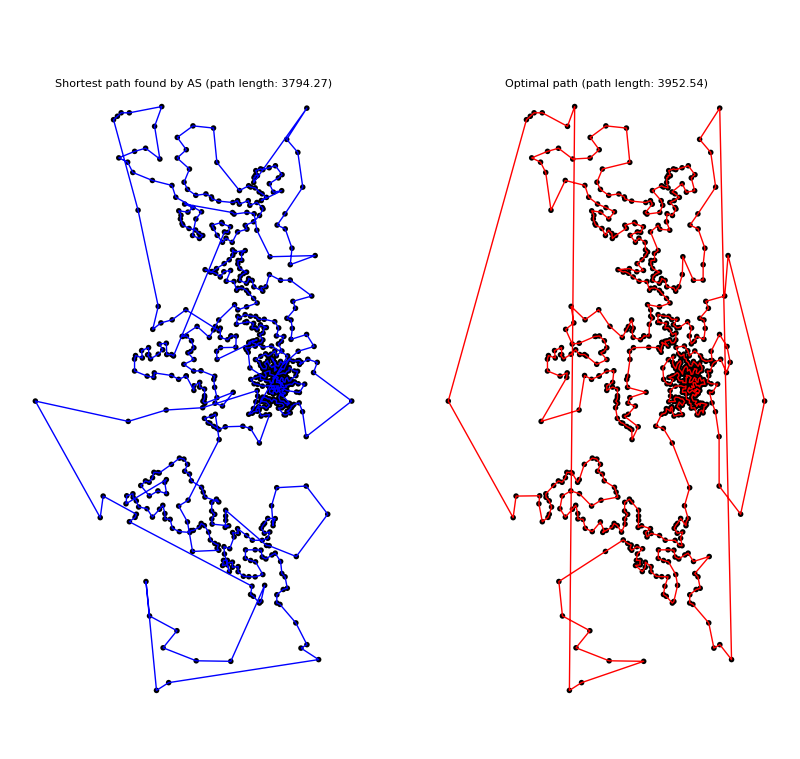

```mathematica
visualizeTspPath[tspFile_, path_, lineColor_] := Module[
{ 
nodes = Map[ {ToExpression[#[[2]]], ToExpression[#[[3]]]} &,  
Map[StringSplit, tspFile]],
lines= {}
 },
lines = Map[ nodes[[ Floor[ # ] ]]&, path];
{ {PointSize[0.01], Point[nodes], }, {lineColor, Thick, Line[lines]}}
];

shortestPathLength = Min[shortestPathLengths];
shortestPathCycles = Position[pathLengths, shortestPathLength];

shortestPaths = Table[ pathHistory[[ shortestPathCycles[[i]][[1]], shortestPathCycles[[i]][[2]] ]], {i, 1, Length[shortestPathCycles]}];

(*
Do[
Print[
Graphics[visualizeTspPath[tspFile, shortestPaths[[i]], Blue], PlotLabel -> "Shortest path found by AS (path length: " <> ToString[shortestPathLength] <> ")"  <> plotlabeladd]
]
,{i, 1, Length[shortestPaths]}]
*)

labelStyleDirective = Directive[Bold, FontSize-> 18];

g1 = Graphics[visualizeTspPath[tspFile, shortestPaths[[1]], Blue], PlotLabel -> "Shortest path found by AS (path length: " <> ToString[shortestPathLength] <> ")", LabelStyle->labelStyleDirective];
g2 = Graphics[visualizeTspPath[tspFile, knownShortestPath, Red], PlotLabel -> "Optimal path (path length: " <> ToString[knownShortestPathLength] <> ")", LabelStyle->labelStyleDirective];

GraphicsRow[ {g1,g2}, ImageSize->Full, PlotLabel-> plotlabeladd, LabelStyle->labelStyleDirective]
```